```mathematica
a=0.00767409187994837
Quantile[NormalDistribution[0,1],1-a]
```

0.00767409

2.42406

Solve::ivar: 10 不是一个有效的变量.

Solve[84.2406,10]

```mathematica
α=0.00767409187994837
```

0.00767409

```mathematica
σ=0.857835
Quantile[LogNormalDistribution[Log[60],σ],1-α]
```

0.857835

480.

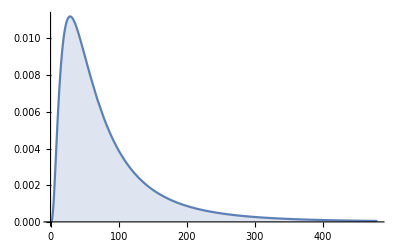

Log[60]

0.857835

```mathematica
Plot[PDF[LogNormalDistribution[Log[60],σ],x],{x,0,480},Filling->Bottom]
μ=Log[60]
σ
```

```mathematica
N[μ]
```

```mathematica
4.0943445622221
0.857835
```

```mathematica
Integrate[PDF[LogNormalDistribution[Log[60],σ],x],{x,352,Infinity}]
```

0.01958

```mathematica
MILES=1.609344
(0.5*30+220)*MILES
(1*30+220)*MILES
(1.5*30+220)*MILES
(2*30+220)*MILES
(2.5*30+220)*MILES
```

1.60934

378.196

402.336

426.476

450.616

474.756

```mathematica
{Integrate[PDF[LogNormalDistribution[Log[60],σ],x],{x,354.055,378.196}],
Integrate[PDF[LogNormalDistribution[Log[60],σ],x],{x,378.196,402.336}],
Integrate[PDF[LogNormalDistribution[Log[60],σ],x],{x,402.336,426.476}],
Integrate[PDF[LogNormalDistribution[Log[60],σ],x],{x,426.476,450.616}],
Integrate[PDF[LogNormalDistribution[Log[60],σ],x],{x,450.616,474.756}],
Integrate[PDF[LogNormalDistribution[Log[60],σ],x],{x,474.756,580}]}
```

{0.00333021,0.00266243,0.0021466,0.00174412,0.00142724,0.0038603}

```mathematica
{0.5,1,1.5,2,2.5,3}
```

{0.5,1,1.5,2,2.5,3}

```mathematica
Ration={0.0033302082582459805,0.0026624348132323777,0.0021466027985346152,0.001744121620558189,0.0014272369830181067,0.003860299284803687}
```

{0.00333021,0.00266243,0.0021466,0.00174412,0.00142724,0.0038603}

```mathematica
Time={0.5,1,1.5,2,2.5,3}
Time.Ration
```

{0.5,1,1.5,2,2.5,3}

0.0261847

```mathematica
Ktime=24/0.026184676693229998
```

916.567

```mathematica
NumberOfCar=Ktime*Ration
```

{3.05236,2.4403,1.9675,1.5986,1.30816,3.53822}

```mathematica
NumberOfCar
```

{3.05236,2.4403,1.9675,1.5986,1.30816,3.53822}

```mathematica
Total[NumberOfCar]
```

13.9051

```mathematica
NeedRation=Integrate[PDF[LogNormalDistribution[Log[60],σ],x],{x,354.055,580}]
```

0.0151709

```mathematica
TotalCar=233760558
```

233760558

```mathematica
TotalCar*NeedRation
```

3.54636×10^6

```mathematica
IntegerPart[TotalCar*NeedRation]
```

3546358

```mathematica
StationNum=TotalCar*NeedRation/26.905143625300852
```

131810.

```mathematica
IntegerPart[StationNum]
```

131809

```mathematica
TotalCar*NeedRation/StationNum
```

26.9051

```mathematica
131809/49
```

131809/49

```mathematica
N[131809/49]
```

2689.98

```mathematica
IntegerPart[2689.9795918367345]
```

2689

```mathematica
354*10^4/49
```

3540000/49

```mathematica
N[3540000/49]
```

72244.9

```mathematica
StateName={"AL","AR","AZ","CA","CO","CT","DC","DE","FL","GA","HI","IA","ID","IL","IN","KS","LA","MA","MD","ME","MI","MN","MO","MS","MT","NC","ND","NE","NH","NJ","NM","NV","NY","OH","OR","PA","RI","SC","SD","SO","TN","TX","UT","VA","VT","WA","WI","WV","WY"}
```

{AL,AR,AZ,CA,CO,CT,DC,DE,FL,GA,HI,IA,ID,IL,IN,KS,LA,MA,MD,ME,MI,MN,MO,MS,MT,NC,ND,NE,NH,NJ,NM,NV,NY,OH,OR,PA,RI,SC,SD,SO,TN,TX,UT,VA,VT,WA,WI,WV,WY}

```mathematica
StateRation={0.020185272,0.016389807,0.021011603,0.130493081,0.015973465,0.011949599,0.00182757,0.003949741,0.06940876,0.031263255,0.011514428,0.005371404,0.039980197,0.020589332,0.008662424,0.015141231,0.012594342,0.020371075,0.017460064,0.003615936,0.028702405,0.018394044,0.019862503,0.007428728,0.003898439,0.03133556,0.002150127,0.006187627,0.004678567,0.025163793,0.005842317,0.00925446,0.043215991,0.041475579,0.012186765,0.013108834,0.041003066,0.003854666,0.016261341,0.003221383,0.020745145,0.073225935,0.00831115,0.028650812,0.002028474,0.025939371,0.019085025,0.0051655,0.00186980}
```

{0.0201853,0.0163898,0.0210116,0.130493,0.0159735,0.0119496,0.00182757,0.00394974,0.0694088,0.0312633,0.0115144,0.0053714,0.0399802,0.0205893,0.00866242,0.0151412,0.0125943,0.0203711,0.0174601,0.00361594,0.0287024,0.018394,0.0198625,0.00742873,0.00389844,0.0313356,0.00215013,0.00618763,0.00467857,0.0251638,0.00584232,0.00925446,0.043216,0.0414756,0.0121868,0.0131088,0.0410031,0.00385467,0.0162613,0.00322138,0.0207451,0.0732259,0.00831115,0.0286508,0.00202847,0.0259394,0.019085,0.0051655,0.0018698}

```mathematica
StateStationNum=IntegerPart[TotalCar*NeedRation/26*StateRation]
```

{2753,2235,2865,17799,2178,1629,249,538,9467,4264,1570,732,5453,2808,1181,2065,1717,2778,2381,493,3914,2508,2709,1013,531,4274,293,843,638,3432,796,1262,5894,5657,1662,1788,5592,525,2218,439,2829,9987,1133,3907,276,3538,2603,704,255}

```mathematica
TotalCar
StateCarNum=IntegerPart[TotalCar*NeedRation*StateRation]
```

233760558

{71584,58124,74514,462775,56647,42377,6481,14007,246148,110870,40834,19048,141784,73017,30720,53696,44664,72243,61919,12823,101789,65231,70439,26344,13825,111127,7625,21943,16591,89239,20718,32819,153259,147087,43218,46488,145411,13670,57668,11424,73569,259685,29474,101606,7193,91990,67682,18318,6630}

```mathematica
Total[StateCarNum]
```

3546333

```mathematica
data=Map[{#[[1]],#[[2]],#[[3]],1.2+(3.7+RandomReal[{-1,1}])#[[1]]-2#[[2]]+23.4#[[3]]}&,RandomReal[10,{100,3}]]
```

{{0.843099,9.16922,1.52556,21.8611},{6.95981,4.71365,1.63257,51.3708},{8.5361,7.52145,9.81482,239.492},{6.96043,0.367571,7.70345,201.704},{4.51014,4.32243,0.836799,26.2261},{3.96126,0.406336,1.37201,46.9663},{7.38992,3.03863,9.60402,246.781},{9.83943,9.05385,2.99334,94.8301},{0.30372,9.71148,7.73879,164.064},{5.43241,7.47773,0.618428,25.4266},{5.8283,1.03209,1.88933,63.5982},{7.34499,3.82768,6.60651,168.948},{5.73542,9.84667,2.64197,66.298},{5.12872,9.25911,4.81708,112.031},{1.33619,1.46916,4.96279,119.402},{5.69515,9.91055,7.48208,175.116},{4.65113,9.92006,5.87222,133.246},{4.74525,7.57741,4.74985,119.309},{1.24184,8.0212,5.68539,123.04},{5.9766,4.81474,4.34196,110.764},{3.84021,1.19778,9.98597,246.994},{7.12489,2.72331,0.175119,23.8629},{8.30056,8.46079,1.38369,46.2505},{4.56422,6.08272,2.25167,59.7952},{5.02701,2.59597,1.45137,47.341},{9.8891,3.06233,9.10221,237.195},{0.819615,3.18533,0.325279,5.41494},{2.3019,5.04579,2.25277,50.1028},{7.73482,4.41082,0.73585,43.5301},{4.13232,3.26378,2.56578,71.9027},{0.609744,9.63353,5.63818,116.451},{4.39854,9.65186,7.35552,167.255},{2.29177,0.795317,6.78804,165.079},{7.74762,8.24305,4.08481,104.729},{4.07872,6.46367,9.47377,223.957},{2.15061,8.12314,5.52526,123.583},{4.22608,5.7316,8.81515,214.358},{7.7475,6.71318,1.4177,56.1812},{1.24644,7.65873,1.75739,31.7296},{4.05681,7.40257,5.08713,124.169},{2.89725,3.0254,9.67173,229.444},{9.64089,4.00045,4.85757,150.924},{9.18364,0.159382,8.37174,230.317},{6.64579,3.92457,9.66034,246.484},{4.63909,1.51059,8.84211,221.482},{6.40025,0.160842,0.534281,33.8949},{3.02451,6.9234,4.69426,106.605},{5.48556,3.8939,1.24508,38.0043},{3.02222,3.49989,1.50827,39.4925},{1.74337,3.60146,4.8054,113.784},{0.942399,2.74792,4.85581,112.7},{7.31461,0.836847,5.38688,156.699},{8.67007,2.14719,4.68742,139.183},{3.00964,8.45242,1.93464,38.5847},{4.40036,6.45964,2.8282,68.4371},{9.21188,7.81496,3.57114,99.9337},{1.21803,6.95752,9.7568,221.303},{8.19309,9.96864,5.96367,153.776},{7.00495,0.832913,0.359825,29.7799},{7.53158,6.24505,3.34736,96.1763},{7.41236,4.47009,7.48308,190.956},{3.48575,2.93708,8.24985,199.536},{3.33526,6.77235,8.19784,189.054},{8.75505,3.22635,0.0442144,21.9479},{2.2834,2.98457,0.215871,9.81467},{7.67226,9.53828,8.73006,215.076},{7.70975,8.95216,2.41676,71.0929},{7.19643,4.87565,4.76145,134.297},{8.48996,9.4969,3.97061,109.076},{5.94481,9.56495,1.72317,43.3796},{8.94236,5.83164,8.67868,234.417},{0.845647,5.56817,2.3746,48.1158},{9.50492,4.60088,8.34174,219.674},{2.41625,1.38337,8.08741,195.478},{8.46975,6.36572,3.09579,89.0673},{9.36392,2.04626,4.38358,135.223},{9.66969,7.92213,0.27322,24.7654},{8.93348,0.354599,2.51838,89.9238},{8.41097,4.28999,9.97965,251.595},{2.09032,5.71285,2.66967,61.0947},{2.68058,1.77093,1.6981,47.0859},{9.97787,9.19089,8.42362,220.047},{7.41767,4.89465,0.565406,26.6582},{2.60577,9.4281,2.23091,44.1082},{5.55931,8.8674,1.55489,42.9128},{3.71916,2.81138,9.70001,238.084},{1.7956,4.55213,8.75238,202.115},{2.7432,7.83245,1.79929,37.8656},{2.93344,4.30173,9.40622,221.615},{0.399302,4.25985,4.00566,87.946},{0.52727,2.88365,0.570437,11.179},{9.69721,8.5594,1.00158,44.7738},{3.07269,4.24942,9.46873,223.815},{6.27814,2.3655,7.30647,196.881},{1.39002,4.8984,9.26688,213.509},{4.85841,2.13594,9.70541,245.122},{8.52257,7.1823,2.89673,92.0297},{4.6563,1.94089,5.48405,142.703},{7.0699,3.31067,9.87246,257.951},{7.69013,2.10729,4.45012,133.286}}

```mathematica
lm=LinearModelFit[data,{x,y,z},{x,y,z}]
```

FittedModel[0.825299+3.80296 x-1.89269 y+23.293 z]

Plot::plln: {{x,0,1},{y,0,1},{z,0,1}} 中的极限值 {y,0,1} 不是一个机器精度实数.

Plot[lm,{{x,0,1},{y,0,1},{z,0,1}}]

```mathematica
AllCarNum={2419523,2421798,2463697,2521433,2573961,2631093}
```

{2419523,2421798,2463697,2521433,2573961,2631093}

```mathematica
ElecCarWorld={182600,388100,715400,1262600,2014200,3283146}
AllCarNum={2419523,2421798,2463697,2521433,2573961,2631093}
Population={4593.7,4614.7,4645.4,4687.8,4739.6,4792.5}
GDP={174087,176540,191028,243181,255294,272357}
```

{182600,388100,715400,1262600,2014200,3283146}

{2419523,2421798,2463697,2521433,2573961,2631093}

{4593.7,4614.7,4645.4,4687.8,4739.6,4792.5}

{174087,176540,191028,243181,255294,272357}

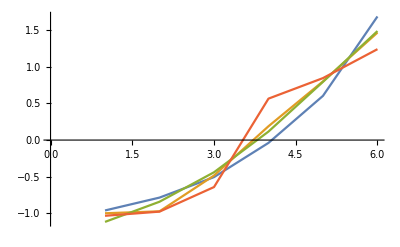

```mathematica
ListLinePlot[{Standardize[ElecCarWorld],Standardize[AllCarNum],Standardize[Population],Standardize[GDP]},PlotLegends->{"one","two","three"}]
```

```mathematica
ListLinePlot[Table[Accumulate[RandomReal[{-1,1},250]],{3}],Filling->Axis,PlotLegends->{"one","two","three"}]
```

```mathematica
Table[Accumulate[RandomReal[{-1,1},250]],{3}];
```